```mathematica
(*syntax, this is how you make a comment!*)
```

```mathematica
!x (*not x*) Not[x]
x! (*x factorial*)Factorial[x]
[x,y,z] (*list*)List[x,y,z]
x+y+z Plus[x,y,z]
∫k[x]ⅆx  same as Integrate[k[x],x]
(term) (*parentheses for grouping*)
f[x] (*square brackets fo functions*)
{a,b,c} (*curly braces for lists, can have nested lists by putting curly baraces in list*)
v[[i]](*double brackets for indexing, where v has been defined as a list or range (Part[v,i]*)
Range[10] (*just like pythons arange()*)
Sin[2] (*this will return Sin(2)*)
N[Sin[2]] (*this will give the numerical solution to sin(2) = 0.909...*)
Plot[{Sin[x], Cos[x]}, {x,1,10}] (*plot has square brackets around the total command to plot, curly braces around the function(s) to plot, included in this example is the x range, which is like a list with {}*)
(*IT KNOWS SYMBOLIC ANALYSIS!!!!!!!!*)
Expand[] (*this will expand something factored*)
Factor[](*this will do the opposite of expand*)
expr/.x->value (*replace x by value in the expression expr*)
expr/.{x->xvalue,y->yvalue} (*this will replace x and y in the expression with the given values*)
x = 3 (*this declares the value of x for the rest of the page, and anywhere an x is after this will be evaluated as 3*)
x=. (*this will remove any value defined for x, so it will evaluate only as symbol x*)
```

```mathematica
Simplify[x^2+2x+1] (*writes in factord form*)
```

```mathematica
(1+x)^2
```

```mathematica
D[x^n,x] (*differential*)
```

n x^(-1+n)

```mathematica
D[x^n,{x,3}] (*third deriv*)
```

(-2+n) (-1+n) n x^(-3+n)

```mathematica
D[x^2+y^2,x](*partial derivs, assumes x and y independent*)
```

2 x

```mathematica
D[x^2+y^2,{{x,y}}] (*gradiant*)
```

{2 x,2 y}

```mathematica
D[x^2+y^2,{{x,y}},2] (*hessian*)
```

General::ivar: 2 is not a valid variable.

∂_2 {2 x,2 y}

```mathematica
Integrate[x^n,x] (*can plug in any expression eg x^n, wrt is the dx*)
```

x^(1+n)/(1+n)

```mathematica
Integrate[f,x] (*indefinite integral*)
Integrate[f,x,y] (*multiple integral*)
Integrate[f,{x,xmin,xmax}] (*definite integral*)
Integrate[f,{x,xmin,xmax},{y,ymin,ymax}] (*definite multiple integral*)
```

```mathematica
Integrate[x^x,{x,0,1}] (*cant give formula for this*)
```

∫_0^1 x^x ⅆx

```mathematica
N[%] (*but can give numerical solution. "%" means input the expression from above line into this, so i dont have to copy and past the integral line of code*)
```

0.783431

```mathematica
DSolve[y'[x]+y[x] == 1, y[x],x] (*this gives a rule for y[x]*)
```

{{y[x]→1+ⅇ^-x C[1]}}

```mathematica
(*DSolve[eqn,y[x],x] solves DE for y[x]
DSolve[eqn,y,x] solves DE for functiony*)
DSolve[{y[x]==-z'[x],z[x]==-y'[x]},{y,z},x] (*solves 2 DE simultantoeously*)
```

{{y→Function[{x},1/2 ⅇ^-x (1+ⅇ^(2 x)) C[1]-1/2 ⅇ^-x (-1+ⅇ^(2 x)) C[2]],z→Function[{x},-1/2 ⅇ^-x (-1+ⅇ^(2 x)) C[1]+1/2 ⅇ^-x (1+ⅇ^(2 x)) C[2]]}}

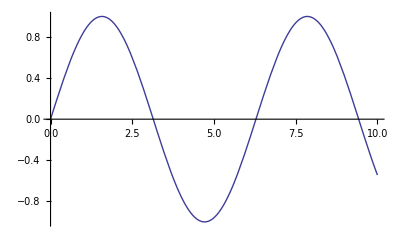

```mathematica
Plot[Sin[x],{x,0,10}] (*plots function*)
```

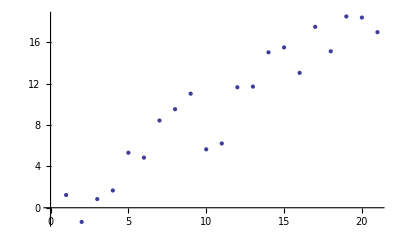

```mathematica
datapts=Table[x+RandomReal[{-4,4}],{x,0,20}];
ListPlot[datapts] (*plots data as points*)
```

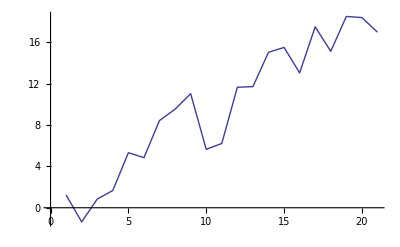

```mathematica
ListLinePlot[datapts] (*plot data joined by line*)
```

```mathematica
Plot3D[Sin[x] Cos[y],{x,0,5},{y,1,10}] (*plots function in 3d*)
```

-Graphics3D-

```mathematica
GraphicsGrid[{{Plot3D[Sin[x] Cos[y],{x,0,5},{y,1,10}],Plot3D[Sin[x]*Cos[y],{x,0,5},{y,1,10},ColorFunction->(Hue[#3]&),MeshFunctions->(#3&),Boxed->False,Axes->False]}}] (*customize plots, notice color function and mesh function and boxed and axes true or false*)
```

-Graphics-

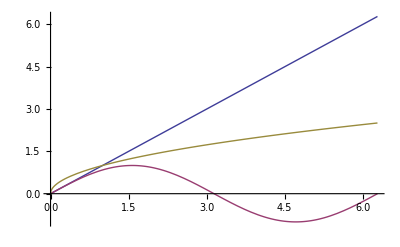

```mathematica
Plot[{x,Sin[x],Sqrt[x]},{x,0,2 Pi}] )(*plot multiple functions in curly braces*)
```

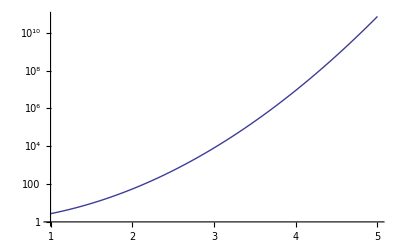

```mathematica
LogPlot[E^x^2,{x,1,5}](*plot of log-scale verticle axis*)
```

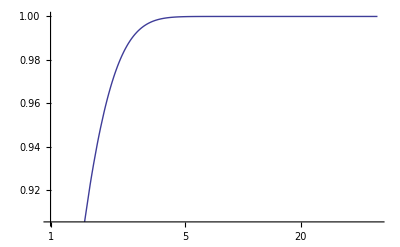

```mathematica
LogLinearPlot[Tanh[x],{x,1,50}](*plot of log-scale horizontal axis*)
```

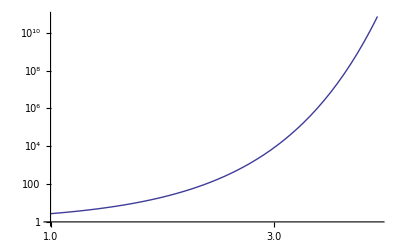

```mathematica
LogLogPlot[E^x^2,{x,1,5}](*loglog plot*)
```

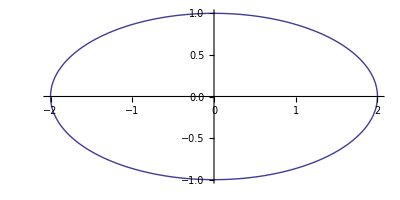

```mathematica
ParametricPlot[{2 Sin[t],Cos[t]},{t,0,2 Pi}] (*parametric curve, can make this a 3d plot by changing command to "ParametricPlot3D[]"*)
```

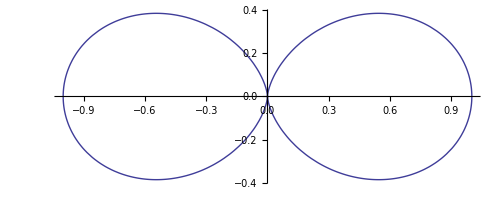

```mathematica
PolarPlot[Cos[t]^2,{t,0,2 Pi}](*plot in polar coords*)
```

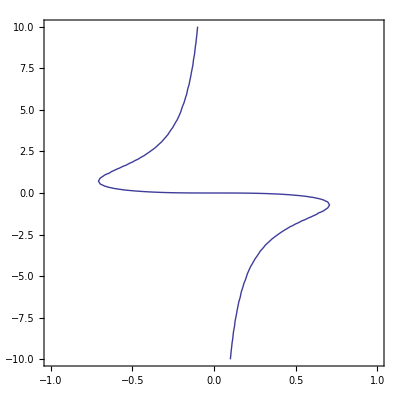

```mathematica
ContourPlot[x^3+x y^2+y==0,{x,-1,1},{y,-10,10}](*for implicitly defined function on contour plot*)
```

```mathematica
(*NDSolve[] takes 3 arguments, 1> function to solve for, 2. y(x), 3. the range for the independent variable*)
ode1={y''[x]+Sin[y[x]]==0,y[0]==2,y'[0]==1};
sol=NDSolve[ode1,y,{x,-10,10}]
```

{{y→InterpolatingFunction[{{-10.,10.}},<>]}}

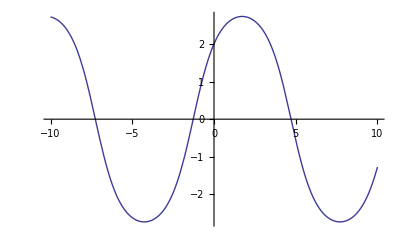

```mathematica
Plot[y[x]/.sol,{x,-10,10}](*plots the solution*)
```

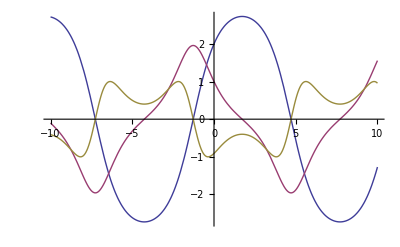

```mathematica
Plot[Evaluate[{y[x],y'[x],y''[x]}/.sol],{x,-10,10}](*plotting a solution with its derivatives. use Evaluate[] to see the plots in different colors*)
```

```mathematica
wws = NDSolve[{D[u[t,x], t,t] == D[u[t,x], x,x] + (1 - u[t, x]^2) (1 + 2 u[t, x]), u[0, x] == E^-x^2, 
Derivative[1,0][u][0, x] == 0, u[t, -10] == u[t, 10]}, 
  u, {t, 0, 10}, {x, -10, 10}]
```

{{u→InterpolatingFunction[{{0.,10.},{-10.,10.}},<>]}}

```mathematica
Plot3D[u[t,x]/.wws,{t,0,10},{x,-10,10}](*plot solution in 3d for t vs x, and give the range for these axes*)
```

-Graphics3D-

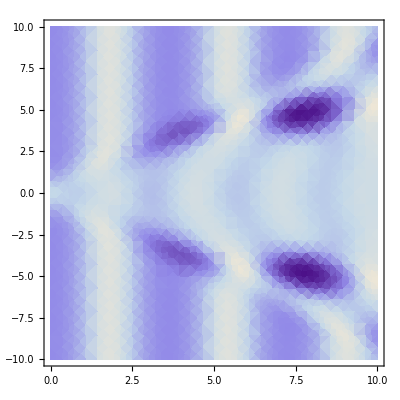

```mathematica
DensityPlot[u[t,x]/.wws,{t,0,10},{x,-10,10}](*just another way of looking at the solution, alternative to 3D plot*)
```

```mathematica
Table[n,{n,1,20}](*Table is a common function that in this case produces a range, list, of numbers for 1 to 20*)
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
Manipulate[n,{n,1,20}](*just switch out Table[] for Manipulate[] and you can see each value with a slider*)
```

```mathematica
Manipulate[Plot[Sin[n x],{x,0,2 Pi}],{n,1,20}] (*it doesnt just have to be a list, Manipulate[] works on alot of expressions*)
(*the plus sign symblo next to the slider opens a panal of additional controls*)
```

```mathematica
Manipulate[Plot[Sin[n x],{x,0,2 Pi}],{n,1,20,Appearance->"Labeled"}](*Appearance lets you see a specific variable without opening the panel*)
```

```mathematica
Manipulate[Plot[Sin[n1 x]+Sin[n2 x],{x,0,2 Pi},PlotRange->2],{n1,1,20},{n2,1,20}](*Manipulate allows you to control more than one variable range*)
```

```mathematica
Manipulate[Plot3D[Sin[n x y],{x,0,3},{y,0,3}],{n,1,5}](*can use Manipulate[] in 3D plots too!*)
```